# FEBRUARY 2021

### Mathematica Notebook by Lee Altenberg

## DATA

```mathematica
may2020={X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,X,1,3,3,3,1};
```

```mathematica
apr2020//Dim
```

{30}

```mathematica
Map[Total,jun2020]
```

{0,1,1,2,9,9,2,1,6,4,7,15,17,5,8,4,4,18,27,14,11,4,3,16,17,17,6,27,2,18}

```mathematica
mar2020={0,0,0,0,1,0,0,1,0,0,0,0,2,3,3,1,5,6,17,10,10,20,14,9,17,17,35,28,31,22,31};
apr2020={28,39,22,15,18,22,21,9,11,20,14,4,6,11,11,9,20,8,4,2,6,5,3,2,2,1,1,4,4,1};
may2020={0,3,1,3,1,2,0,2,1,2,1,3,0,0,2,1,0,1,1,4,0,1,0,0,0,0,2,3,3,0,0};
jun2020={0,1,1,2,9,9,2,1,6,4,7,15,17,5,8,4,4,18,27,14,11,4,3,16,17,17,6,27,2,18};
jul2020={9,9,9,24,25,7,41,23,36,28,42,21,23,22,29,19,23,20,28,12,25,17,55,60,73,64,28,47,109,124,123};
aug2020={ 87, 45,207,144,173,152, 201,231,152,140,
118,202,355,233,284,220,174,134,261,236,
230,284,244,169,215,277,306,265,310,200,133};
sep2020={181,339,211,271,221,164,105,66,100,169,167,131,114,80,66,102,160,114,110,77,56,63,168,90, 112,127,98,90,87,121};
oct2020={108,87,133,70,52,83,110,101,155,73,
103,42,62,101,91,89,96,83,39,91,
78,102,131,90,121,38,66,62,77,94,68};
nov2020={83,78,89,155,100,122,128,128,64,78,
78,97,110,108, (* 95 *) 53.5, 41.5 , 53,71,107,95,
163,123,114,61,108,120,92,76,57,85};
dec2020={44,63,144,106,133,105,81,53,80,123,
89,198,90,190,57,110,142,130,156 ,204,
134,66,107,129,120,120,95,46,76,108, 188};
jan2021={241,171,149,89,124,143,322,264,250,200,
172,114,106,179,150,165,132,129,65,75,
119,132,134,153,123,71,103,100,115,116,
82};
feb2021={90};
sinceMar2020=Flatten[{mar2020,apr2020,may2020,jun2020,jul2020,aug2020,sep2020,oct2020,nov2020,dec2020,jan2021,feb2021}];
sinceJune2020=Flatten[{jun2020,jul2020,aug2020,sep2020,oct2020,nov2020,dec2020,jan2021,feb2021}];
dataN= Length[sinceJune2020];
dataAllN= Length[sinceMar2020];
```

```mathematica
Dim@jan2021
```

{30}

## TOOLS

```mathematica
Tp = Transpose;
Dim=Dimensions;
Idm = IdentityMatrix;
MF = MatrixForm;
TF=TableForm;
FS = FullSimplify;
LP[ar_]:=ListPlot[ar,PlotRange->All];
LP3[ar_]:=ListPlot3D[ar,PlotRange->All];
LPJ[ar_]:=ListPlot[ar,PlotRange->All,Joined->True];MP[mat_]:=MatrixPlot[mat];
specRad[A_]:= Max[Abs[Eigenvalues[A]]];
eVec[n_]:=ConstantArray[1,n];
iVec[i_,n_]:= Table[If[j==i,1,0],{j,n}];
Lg[ar_]:= Log[2,ar];
```

```mathematica
upperCycleMatrix[n_]:= Table[If[Mod[i+1,n] == Mod[j,n], 1, 0], {i, n},{j,n}];
lowerCycleMatrix[n_]:= Table[If[Mod[i,n] == Mod[j-1,n], 1, 0], {i, n},{j,n}]
```

```mathematica
runningMean[ar_,n_]:= Table[Mean@Take[ar,{i,i+n-1}], {i, 1, Length[ar]-n+1}];
runningSymMean[ar_,k_]:= Block[{n=Length[ar]},Table[Mean@Take[ar,{i-Min[i-1,n-i, Floor[k/2]], i+Min[i-1,n-i, Ceiling[k/2]]}], {i, 1,n}]]
```

```mathematica
rToRt[r_]:= Exp[r/.29];
rToDoublingTime[r_]:= Log[2.]/r
```

```mathematica
cJP[ar_]:= DateListPlot[TimeSeries[ar,{"Jun 1, 2020"}],PlotRange->All ]
```

```mathematica
dateAllPlot[ar_]:= DateListPlot[TimeSeries[ar,{"Mar 1, 2020"}],PlotRange->All ]
```

```mathematica
Optimization`NMinimizeDump`$Methods
```

{Automatic,DifferentialEvolution,MeshSearch,NelderMead,SimulatedAnnealing,RandomSearch,NonlinearInteriorPoint}

## EXPONENTIAL FIT FUNCTIONS

```mathematica
twoExpFunc[t_, date_,c1_,r1_,r2_]:= If[t < date, c1 Exp[t r1],c1 Exp[date r1] Exp[(t-date) r2] ]
```

```mathematica
threeExpFunc[t_, date1_,date2_,c1_,r1_,r2_,r3_]:= 
({d1,d2}=Sort[{date1,date2}];
If[t < d1, c1 Exp[t r1],
If[t < d2,c1 Exp[d1 r1] Exp[(t-d1) r2], 
 c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(t-d2) r3] ]])
```

```mathematica
fourExpFunc[t_, date1_,date2_,date3_,c1_,r1_,r2_,r3_,r4_]:= 
({d1,d2,d3}=Sort[{date1,date2,date3}];
If[t < d1, c1 Exp[t r1],
If[t < d2,c1 Exp[d1 r1] Exp[(t-d1) r2],
If[t<d3 ,
 c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(t-d2) r3], 
c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(d3-d2) r3]Exp[(t-d3) r4] ]] ])
```

### 5 PIECE FITS

```mathematica
fiveExpFunc[t_, date1_,date2_,date3_,date4_,c1_,r1_,r2_,r3_,r4_,r5_]:= 
({d1,d2,d3,d4}=Sort[{date1,date2,date3,date4}];
If[t < d1, c1 Exp[t r1],
If[t < d2,c1 Exp[d1 r1] Exp[(t-d1) r2],
If[t<d3 ,
 c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(t-d2) r3], 
If[t<d4,
c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(d3-d2) r3]Exp[(t-d3) r4], c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(d3-d2) r3]Exp[(d4-d3) r4 ]  Exp[(t-d4) r5]] 
] ]])
```

```mathematica
fiveRtFunc[t_, date1_,date2_,date3_,date4_,c1_,r1_,r2_,r3_,r4_,r5_]:= 
({d1,d2,d3,d4}=Sort[{date1,date2,date3,date4}];
If[t < d1, rToRt[r1],
If[t < d2,rToRt[r2],
If[t<d3 ,
 rToRt[r3], 
If[t<d4,
rToRt[ r4], rToRt[ r5]] 
] ]])
```

### 5+1 PIECE FITS

```mathematica
fiveExpMigFunc[t_, date1_,date2_,date3_,date4_,date5_,c1_,c2_,r1_,r2_,r3_,r4_,r5_]:= 
({d1,d2,d3,d4,d5}=Sort[{date1,date2,date3,date4,date5}];
If[t < d1, c1 Exp[t r1],
If[t < d2,c1 Exp[d1 r1] Exp[(t-d1) r2],
If[t<d3 ,
 c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(t-d2) r3], 
If[t<d4,
c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(d3-d2) r3]Exp[(t-d3) r4], 
If[t < d5,c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(d3-d2) r3]Exp[(d4-d3) r4 ]  Exp[(t-d4) r5] ,
c1 Exp[d1 r1] Exp[(d2-d1) r2] Exp[(d3-d2) r3]Exp[(d4-d3) r4 ]  Exp[(t-d4) r5]] + c2 (1-Exp[(t-d5)r5])/(1-Exp[r5])]
] ]])
```

```mathematica
period5Data = Take[sinceJune2020,{101, Length[sinceJune2020]}];
period5Cycle= Take[Flatten[Table[{w1,w2,w3,w4,w5,w6,w7}, Ceiling[Length[period5Data]/7]]],Length[period5Data]];
```

#### PLOTS

```mathematica
triCalPlot[ar_]:= DateListPlot[Map[TimeSeries[#,{"Jun 1, 2020"}]&,ar],PlotRange->All ,Joined->True, PlotStyle->{Thickness[0.0051],Thickness[0.003],Thickness[0.01]} ]
```

```mathematica
triCalPlotAll[ar_]:= DateListPlot[Map[TimeSeries[#,{"Mar 1, 2020"}]&,ar],PlotRange->All ,Joined->True, PlotStyle->{Thickness[0.0051],Thickness[0.003],Thickness[0.01]} ]
```

```mathematica
calJunPlotL[ar_]:= DateListPlot[Map[TimeSeries[#,{"Jun 1, 2020"}]&,ar],PlotRange->All ]
```

```mathematica
cJP[ar_]:= DateListPlot[TimeSeries[ar,{"Jun 1, 2020"}],PlotRange->All ]
```

# THE CASE DATA TIME SERIES

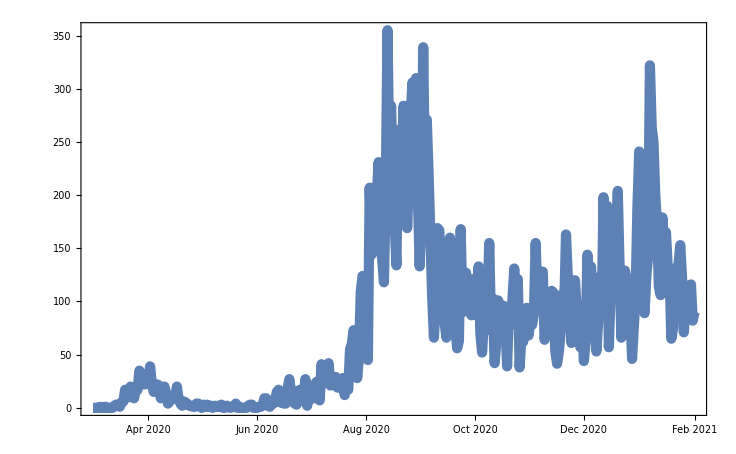

```mathematica
triCalPlotAll[{sinceMar2020}]
```

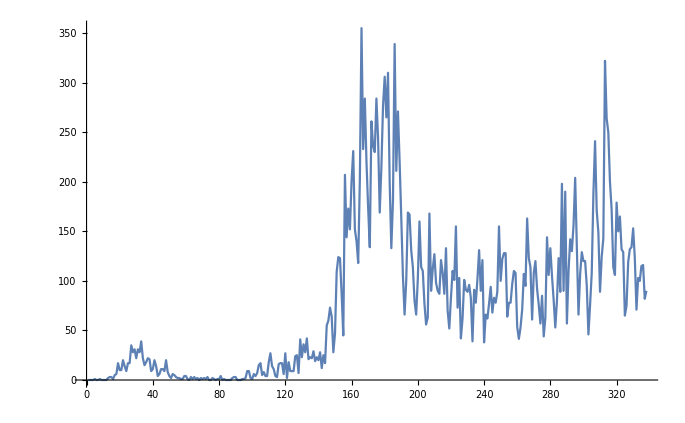

```mathematica
LPJ@sinceMar2020
```

## 7-DAY RUNNING MEAN

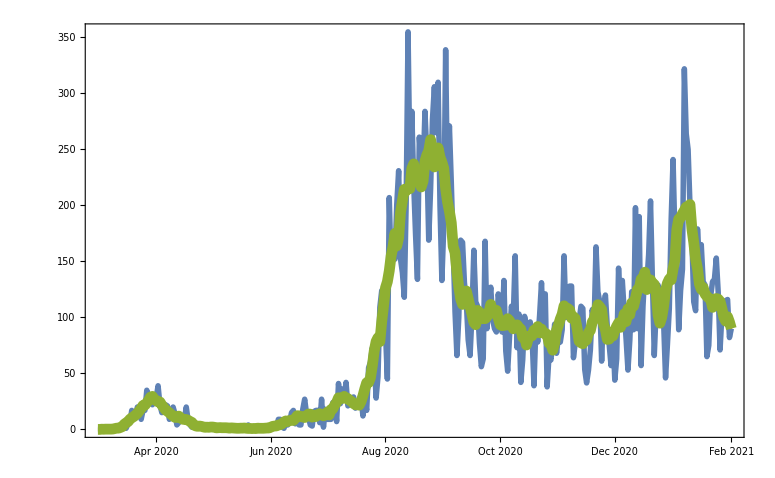

```mathematica
triCalPlotAll[{sinceMar2020,runningSymMean[sinceMar2020,7],runningSymMean[sinceMar2020,7]}]
```

## AUTOCORRELATION

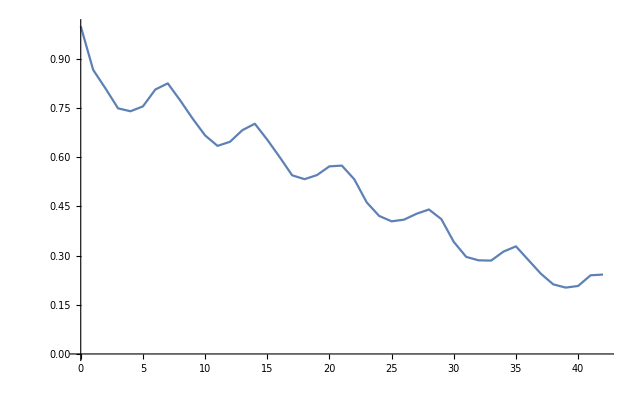

```mathematica
Table[{gap,CorrelationFunction[sinceMar2020, gap]},{gap,0, 42}]//LPJ
```

### We see peaks at multiples of 7. Is there a weekly periodicity?

# DO GROUP

```mathematica
cycleTableAll * runningSymMean[sinceMar2020,7] 1./.bestMeanCycleFitAll[[2]]
```

{0.,0.,0.135297,0.147539,0.311061,0.300188,0.300966,0.233022,0.284767,0.507363,1.16187,1.39977,2.10132,3.00966,4.31091,4.46135,4.65083,9.29494,12.909,13.6586,15.4997,13.2823,12.5297,12.6841,22.0755,26.9068,28.5179,31.4509,26.914,22.4017,18.2651,26.5939,30.6395,29.4184,26.184,18.2922,13.0993,10.9929,15.3625,16.6418,14.409,12.9415,10.0199,9.01762,7.01852,9.42404,11.0427,10.6567,9.78139,6.64113,4.74612,2.70594,3.22741,3.42167,3.60226,3.31062,2.0972,1.42384,1.35297,1.93645,2.64402,2.5516,2.25724,1.28162,1.13907,1.09929,1.54916,1.86637,1.80113,1.65531,1.0486,1.04415,0.845605,1.16187,1.24424,1.20075,1.35435,1.0486,0.949223,0.676484,0.903675,1.08871,0.900565,1.05338,0.699066,0.854301,0.676484,1.03277,1.24424,1.35085,1.50483,1.16511,1.51876,1.86033,3.09831,3.88826,4.65292,5.11642,4.66044,5.03088,5.15819,7.3585,9.79842,9.90621,9.63091,9.08786,9.30239,8.20237,11.7478,13.9977,12.758,14.5968,12.8162,10.3465,7.44132,13.0387,14.3088,15.91,16.8541,12.2337,9.20747,8.79429,15.8789,16.0196,21.3134,22.121,20.2729,18.32,19.1107,28.7885,34.3722,35.4222,33.7082,25.6324,19.6489,16.8275,23.8828,27.3734,26.7167,26.0335,23.1857,22.7814,24.5225,43.1182,51.9472,55.3847,68.1688,65.2462,59.6112,55.3871,80.9435,119.759,132.983,152.289,122.919,107.452,104.855,168.471,217.743,196.773,206.011,180.709,154.913,145.021,219.98,268.446,258.162,280.35,221.021,168.202,154.154,230.179,269.379,266.117,288.325,228.478,188.895,175.04,256.386,291.62,283.228,302.621,226.614,181.302,157.79,222.046,252.737,233.847,222.263,152.28,119.887,94.9614,131.162,144.954,134.034,139.799,115.229,88.6575,74.1596,106.246,118.981,112.27,127.91,97.6362,74.9886,67.9021,102.115,125.047,125.329,134.381,97.0537,78.7855,71.961,102.503,116.337,111.22,114.969,86.6842,75.0836,65.7035,96.435,111.826,109.419,112.411,84.82,67.9644,55.5562,86.1073,93.7849,97.8613,100.523,77.9459,67.2999,60.038,94.8859,107.316,107.617,103.532,80.0431,64.4523,52.0893,78.6197,88.0303,92.6081,106.241,86.6842,74.8937,69.5933,113.992,134.378,129.681,128.362,92.6263,76.4125,66.8873,92.4976,97.9842,92.9082,92.0956,74.6836,60.6554,58.5159,91.2712,119.37,118.124,126.707,103.811,83.152,72.4683,96.9514,110.893,96.5105,97.0615,79.344,63.3132,59.8688,95.1441,118.359,109.419,115.119,96.1216,73.0902,72.8911,105.73,140.6,132.083,141.003,116.395,95.4919,90.7334,139.295,174.661,149.944,157.857,124.434,99.2888,87.6047,125.869,127.068,113.921,120.537,102.763,94.3528,88.3657,138.65,166.107,172.008,182.536,166.261,142.668,127.855,198.938,243.25,238.5,236.409,187.233,136.214,112.973,157.239,178.394,156.098,150.633,118.142,91.7899,80.417,121.222,144.643,130.882,136.939,108.938,88.3727,77.3729,111.41,124.424,116.13,121.109,89.4805,68.3441}

{176835.,{w1→0.932088,w2→0.759379,w3→0.676484,w4→1.03277,w5→1.24424,w6→1.20075,w7→1.20386}}

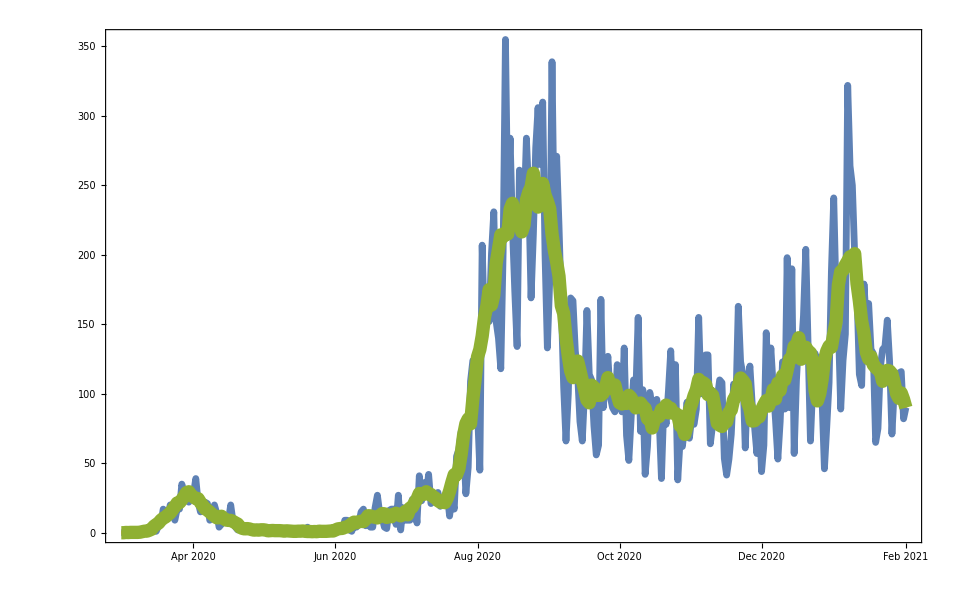

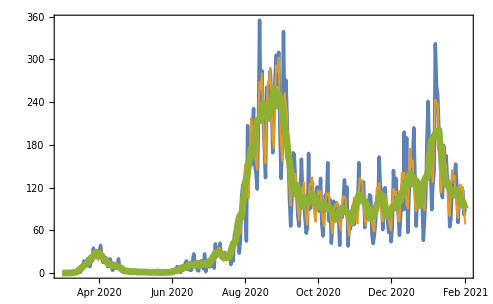

{0.925532,0.754038,0.671726,1.02551,1.23549,1.19231,1.1954}

-Graphics-

```mathematica
cycleTableAll= Take[Flatten[Table[{w1,w2,w3,w4,w5,w6,w7}, Ceiling[Length[sinceMar2020]/7]]],Length[sinceMar2020]];
bestMeanCycleFitAll=NMinimize[Total[(sinceMar2020-cycleTableAll * runningSymMean[sinceMar2020,7])^2], {w1,w2,w3,w4,w5,w6,w7}]
cycleTableAllVals=cycleTableAll/.bestMeanCycleFitAll[[2]];
meanFitDataAll=cycleTableAll * runningSymMean[sinceMar2020,7]/.bestMeanCycleFitAll[[2]];
triCalPlotAll[{sinceMar2020,runningSymMean[sinceMar2020,7],runningSymMean[sinceMar2020,7]}]
triCalPlotAll[{sinceMar2020,meanFitDataAll,runningSymMean[sinceMar2020,7]}]
dailyFactorsRunM={w1,w2,w3,w4,w5,w6,w7} /Mean@{w1,w2,w3,w4,w5,w6,w7}/. bestMeanCycleFitAll[[2]]
ListPlot[dailyFactorsRunM->{"SUN","MON","TUE","WED","THU","FRI","SAT"},LabelingFunction->Above,PlotStyle->{PointSize[0.0251],FontSize->Large},GridLines->Automatic]
```

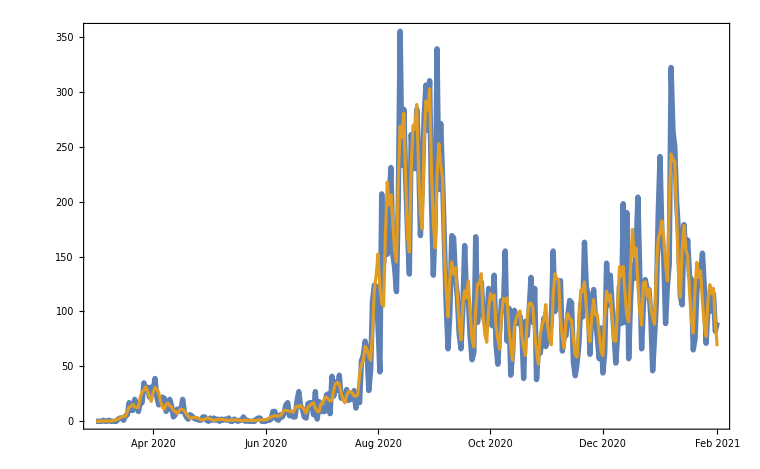

```mathematica
triCalPlotAll[{sinceMar2020,meanFitDataAll}]
```

## VARIANCE — Squared Departures from the 7-day running mean

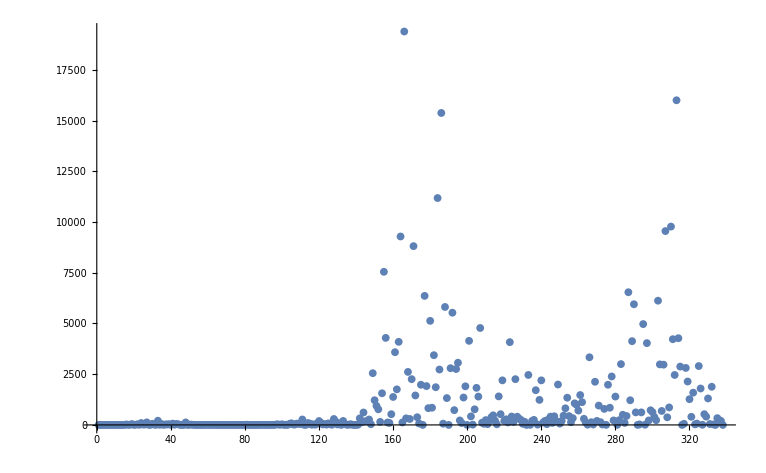

```mathematica
LP[(sinceMar2020- runningSymMean[sinceMar2020,7])^2]
```

### HALF THE VARIANCE IS DUE TO THE DAY-OF-THE-WEEK FACTORS

```mathematica
squaresTotal=Total[(sinceMar2020- runningSymMean[sinceMar2020,7])^2]
```

337809.

```mathematica
squaresCycleTotal=Total[(sinceMar2020- cycleTableAllVals * runningSymMean[sinceMar2020,7])^2]
```

176835.

```mathematica
squaresCycleTotal/squaresTotal
```

0.523477

```mathematica
LP[{(sinceMar2020- runningSymMean[sinceMar2020,7])^2,(sinceMar2020- cycleTableAllVals * runningSymMean[sinceMar2020,7])^2}]
```

```mathematica
meanFitDataAllEd=meanFitDataAll;
meanFitDataAllEd[[1]]= 0.13529678878200513;
meanFitDataAllEd[[2]]= 0.13529678878200513;
```

# TAYLOR’S LAW

```mathematica
rMean=runningSymMean[sinceMar2020, 7];
```

```mathematica
powerPlots=ParallelTable[{k,dateAllPlot@Accumulate[(sinceMar2020- rMean)^2/rMean^(k)]}, {k, 0,2,0.1} ]
```

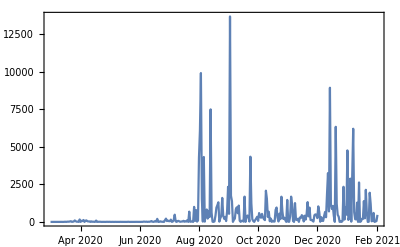
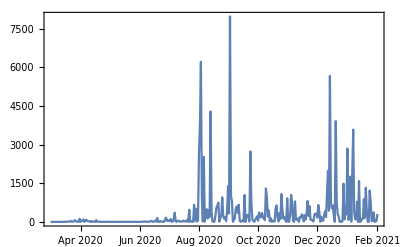
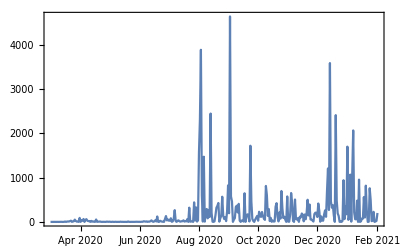
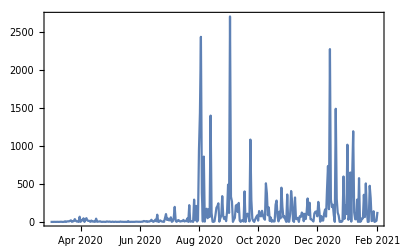
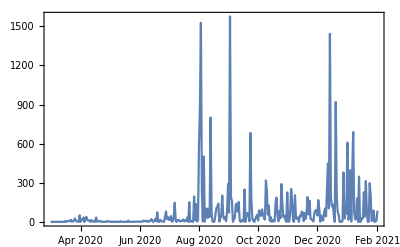
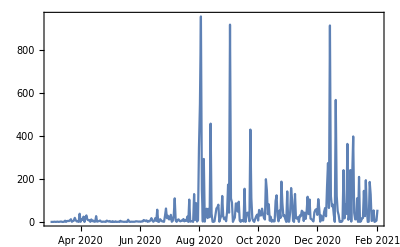
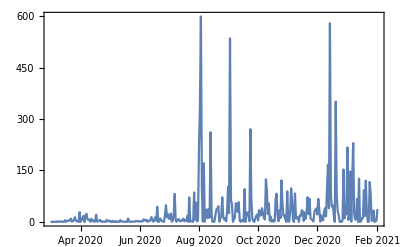
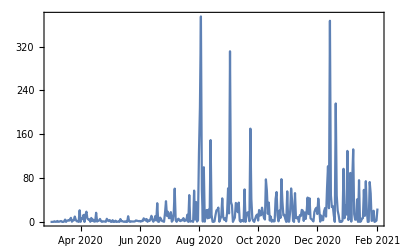
{{0.,-Graphics-},{0.1,-Graphics-},{0.2,-Graphics-},{0.3,-Graphics-},{0.4,-Graphics-},{0.5,-Graphics-},{0.6,-Graphics-},{0.7,-Graphics-},{0.8,-Graphics-},{0.9,-Graphics-},{1.,-Graphics-},{1.1,-Graphics-},{1.2,-Graphics-},{1.3,-Graphics-},{1.4,-Graphics-},{1.5,-Graphics-},{1.6,-Graphics-},{1.7,-Graphics-},{1.8,-Graphics-},{1.9,-Graphics-},{2.,-Graphics-}}

```mathematica
powerPlots=ParallelTable[{k,dateAllPlot[(sinceMar2020- meanFitDataAll)^2/meanFitDataAllEd^(k)]}, {k, 0,2,0.1} ]
```

### How to see uniformity: Accumulate.

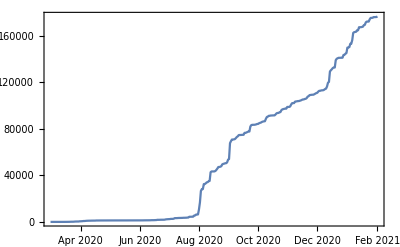
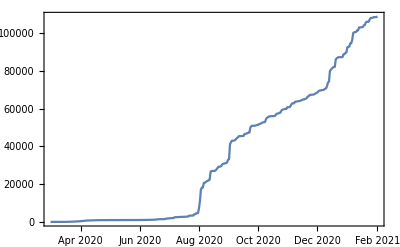
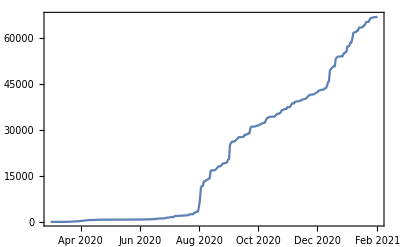
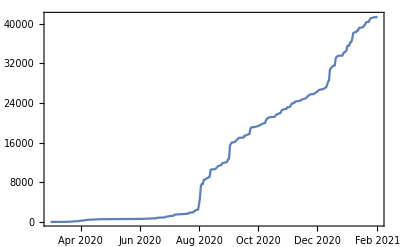
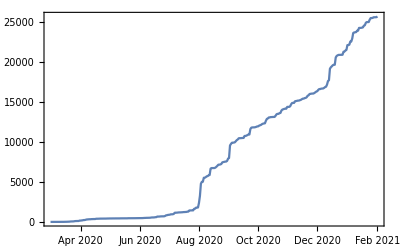
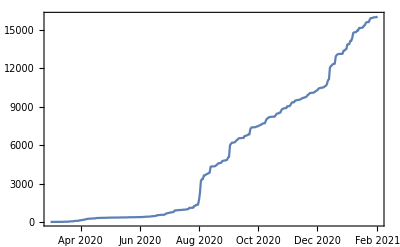
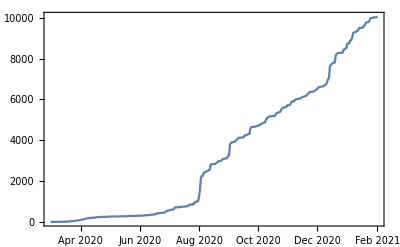
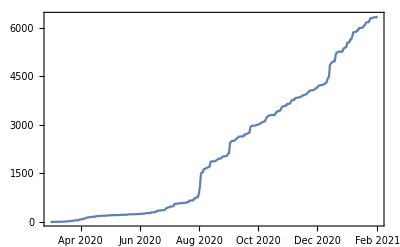
{{0.,-Graphics-},{0.1,-Graphics-},{0.2,-Graphics-},{0.3,-Graphics-},{0.4,-Graphics-},{0.5,-Graphics-},{0.6,-Graphics-},{0.7,-Graphics-},{0.8,-Graphics-},{0.9,-Graphics-},{1.,-Graphics-},{1.1,-Graphics-},{1.2,-Graphics-},{1.3,-Graphics-},{1.4,-Graphics-},{1.5,-Graphics-},{1.6,-Graphics-},{1.7,-Graphics-},{1.8,-Graphics-},{1.9,-Graphics-},{2.,-Graphics-}}

```mathematica
powerPlots=ParallelTable[{k,dateAllPlot@Accumulate[(sinceMar2020- meanFitDataAll)^2/meanFitDataAllEd^(k)]}, {k, 0,2,0.1} ]
```

### Measure the straightness of the curves using Correlation:

```mathematica
Table[{k,Correlation[Range[Length@sinceMar2020],Accumulate[(sinceMar2020- meanFitDataAll)^2/meanFitDataAllEd^(k)]]}, {k, 0,2,0.1} ]//TF
```

0. | 0.947254
0.1 | 0.948233
0.2 | 0.949463
0.3 | 0.951016
0.4 | 0.952985
0.5 | 0.955472
0.6 | 0.958594
0.7 | 0.96247
0.8 | 0.9672
0.9 | 0.972822
1. | 0.979228
1.1 | 0.986029
1.2 | 0.992365
1.3 | 0.996712
1.4 | 0.996865
1.5 | 0.990376
1.6 | 0.975576
1.7 | 0.952726
1.8 | 0.924284
1.9 | 0.893882
2. | 0.864793

### Correlation maximized for exponent 1.4.

# BOOTSTRAP

```mathematica
simData := Table[
RandomVariate@PoissonDistribution@(0.001+sinceMar2020 [[ii]]), {ii, Length[sinceMar2020]}];
```

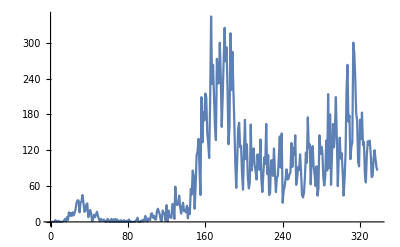

```mathematica
simData//LPJ
```

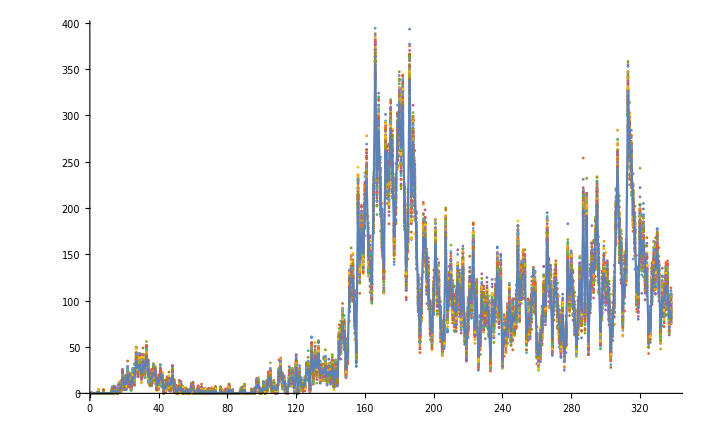

```mathematica
simRuns=Table[simData,100];
Show[ListPlot[simRuns,PlotRange->All], ListPlot[sinceMar2020,Joined->True,PlotRange->All] ]
```

## TWO-PERIOD FIT OF “FIRST WAVE”

```mathematica
twoExpFunc[t_, date_,c1_,r1_,r2_]:= If[t < date, c1 Exp[t r1],c1 Exp[date r1] Exp[(t-date) r2] ]
```

```mathematica
first90=Take[sinceMar2020,90]
```

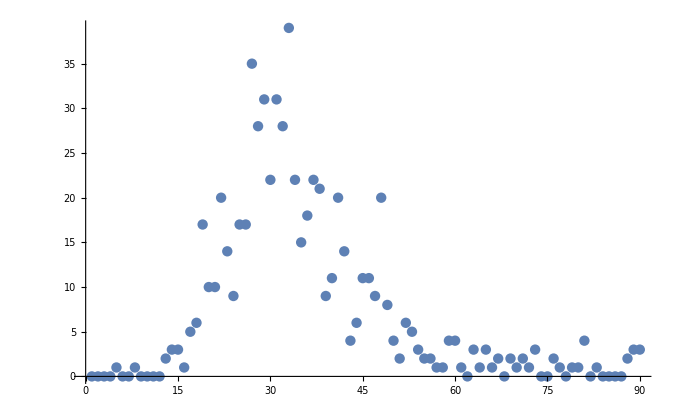

```mathematica
LP@first90
```

```mathematica
bootStrap[ar_]:= Table[
RandomVariate@PoissonDistribution@(0.001+ar [[ii]]), {ii, Length[ar]}]
```

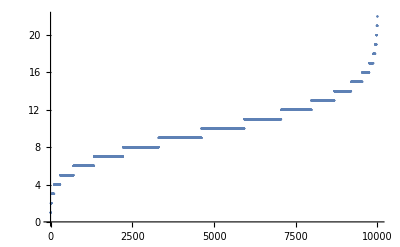

```mathematica
LP@Sort@Table[RandomVariate@PoissonDistribution[10],10000]
```

```mathematica
Variance[Sort@Table[RandomVariate@PoissonDistribution[10],10000]] 1.
```

10.1748

```mathematica
Mean[Sort@Table[RandomVariate@PoissonDistribution[10],10000]] 1.
```

10.0365

```mathematica
bootStrap[first90]
```

{0,0,0,0,3,0,0,0,0,0,0,0,1,4,4,0,4,6,18,7,10,23,16,10,14,9,37,33,37,19,38,32,31,20,15,6,20,22,9,9,18,15,2,5,13,15,14,16,8,1,0,6,2,3,1,2,1,1,2,4,1,0,3,1,4,0,5,0,3,2,3,1,4,0,0,1,1,0,0,1,1,0,1,0,0,0,0,2,1,3}

## BEST FIT OF A 2-PIECE EXPONENTIAL MODEL

```mathematica
bestFit90=Table[NMinimize[Total[(first90- Table[twoExpFunc[t, break, c1, r1,r2],{t, Length[first90]}])^2], {c1,r1,r2},Method->"DifferentialEvolution"],{break,10,40}]
```

{{5986.99,{c1→8.69406×10^-6,r1→1.4366,r2→-0.0170374}},{5755.43,{c1→0.0000849585,r1→1.10381,r2→-0.018669}},{5471.17,{c1→4.38657×10^-6,r1→1.2634,r2→-0.0202706}},{5167.56,{c1→4.20415×10^-6,r1→1.17396,r2→-0.0220528}},{4893.17,{c1→0.0000374764,r1→0.937836,r2→-0.0240281}},{4593.93,{c1→6.14722×10^-6,r1→0.999146,r2→-0.025715}},{4299.98,{c1→0.0000699828,r1→0.78779,r2→-0.0276551}},{3870.51,{c1→3.35592×10^-6,r1→0.924211,r2→-0.0304188}},{3470.61,{c1→6.45827×10^-11,r1→1.48019,r2→-0.0334936}},{3137.55,{c1→0.0000318548,r1→0.714601,r2→-0.0359789}},{3021.5,{c1→0.000391004,r1→0.55482,r2→-0.0380997}},{2813.48,{c1→0.00247921,r1→0.442016,r2→-0.0406812}},{2549.15,{c1→0.00595833,r1→0.383941,r2→-0.0438927}},{2412.76,{c1→0.028584,r1→0.299835,r2→-0.0464552}},{2230.79,{c1→0.0615778,r1→0.256467,r2→-0.0497279}},{1926.88,{c1→0.0766248,r1→0.239329,r2→-0.0545429}},{1629.07,{c1→0.103985,r1→0.220087,r2→-0.0601043}},{1303.92,{c1→0.133902,r1→0.204387,r2→-0.0671875}},{1216.83,{c1→0.264919,r1→0.173079,r2→-0.0726577}},{1190.78,{c1→0.444451,r1→0.149427,r2→-0.07861}},{1252.93,{c1→0.689352,r1→0.129605,r2→-0.0844452}},{1267.66,{c1→0.91575,r1→0.11641,r2→-0.0928612}},{1363.67,{c1→1.19932,r1→0.104145,r2→-0.101621}},{1498.89,{c1→1.50888,r1→0.0937171,r2→-0.111769}},{1826.78,{c1→1.96866,r1→0.0818022,r2→-0.115719}},{2135.31,{c1→2.41282,r1→0.0724004,r2→-0.11985}},{2366.98,{c1→2.78523,r1→0.0655461,r2→-0.127799}},{2574.75,{c1→3.12858,r1→0.0598997,r2→-0.138355}},{2818.48,{c1→3.50037,r1→0.0544039,r2→-0.146797}},{3102.39,{c1→3.90926,r1→0.0489106,r2→-0.149687}},{3311.71,{c1→4.23681,r1→0.0447936,r2→-0.159182}}}

```mathematica
r1->0.14942707507311212,r2->-0.0786099898926045
```

```mathematica
Solve[Exp[t 0.14942707507311212] == 2, t]
```

{{t→4.6387}}

```mathematica
Solve[Exp[t * 0.0786099898926045] == 2, t]
```

{{t→8.81755}}

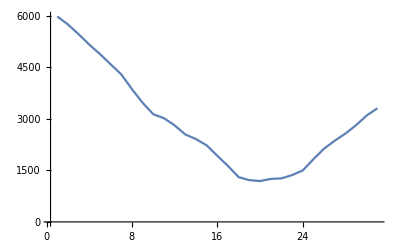

```mathematica
LPJ@Map[First,bestFit90]
```

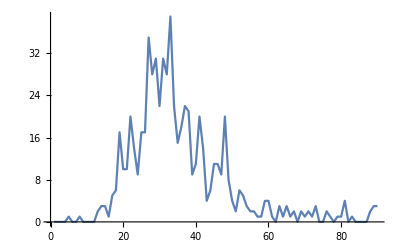

```mathematica
LPJ@first90
```

```mathematica
NMinimize[(first90 - Table[twoExpFunc[t, break,c1,r1,r2],{t,Length[first90]}])^2,{break,c1,r1,r2}]
```

# JUNE and AFTER

{175532.,{w1→0.75921,w2→0.675557,w3→1.03311,w4→1.24438,w5→1.2006,w6→1.20466,w7→0.93188}}

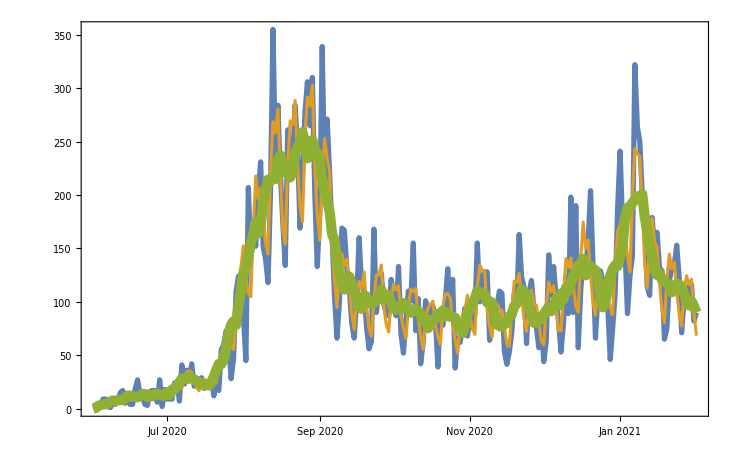

```mathematica
cycleTable= Take[Flatten[Table[{w1,w2,w3,w4,w5,w6,w7}, Ceiling[Length[sinceJune2020]/7]]],Length[sinceJune2020]];
bestMeanCycleFit=NMinimize[Total[(sinceJune2020-cycleTable * runningSymMean[sinceJune2020,7])^2], {w1,w2,w3,w4,w5,w6,w7}]
cycleTableVals=cycleTable/.bestMeanCycleFit[[2]];
meanFitData=cycleTable * runningSymMean[sinceJune2020,7]/.bestMeanCycleFit[[2]];
triCalPlot[{sinceJune2020,meanFitData,runningSymMean[sinceJune2020,7]}]
```

{278268.,{c1→2.81586,r1→0.0361255,r2→0.0993961,r3→0.0126751,r4→-0.158032,r5→0.00285887,w1→1.44192,w2→1.30574,w3→1.94489,w4→2.23397,w5→2.15069,w6→2.27386,w7→1.78711}}

{19.1872,6.97358,54.6856,-4.38611,242.455}

{103,94,140,161,155,165,130,105,95,143,164,159,168,132,107}

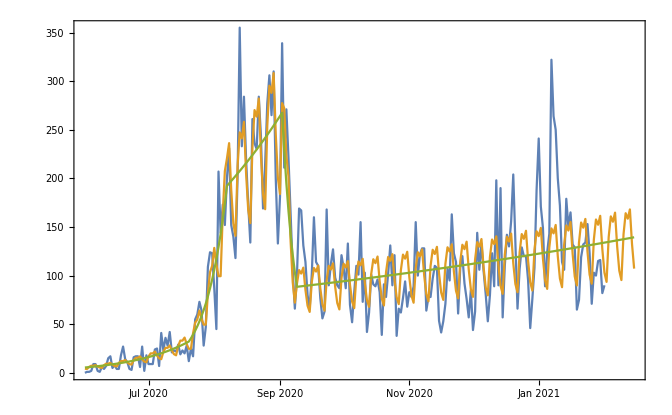

```mathematica
bestFit94101=NMinimize[Total[(sinceJune2020-cycleTable * Table[fiveExpFunc[t, 50,68,94,101, c1, r1,r2,r3,r4,r5],{t, Length[sinceJune2020]}])^2], {c1,r1,r2,r3, r4,r5,w1,w2,w3,w4,w5,w6,w7}]
Log[2.]/{r1,r2,r3,r4,r5} /.bestFit94101[[2]]
cycleTable= Take[Flatten[Table[{w1,w2,w3,w4,w5,w6,w7}, Ceiling[Length[sinceJune2020]/7]]],Length[sinceJune2020]];
cycleTableProj =  Take[Flatten[Table[{w1,w2,w3,w4,w5,w6,w7},2+ Ceiling[Length[sinceJune2020]/7]]],Length[sinceJune2020]+14];fit5TabCyc= (cycleTable * Table[fiveExpFunc[t,50,68,94,101, c1, r1,r2,r3,r4,r5],{t,1, dataN}]) /. bestFit94101[[2]];
fit5TabCycProj= (cycleTableProj * Table[fiveExpFunc[t,50,68,94,101, c1, r1,r2,r3,r4,r5],{t,1, dataN+14}]) /.bestFit94101[[2]];
fit5TabCycMean= (Mean@cycleTableProj * Table[fiveExpFunc[t,50,68,94,101, c1, r1,r2,r3,r4,r5],{t,1, dataN+14}]) /.  bestFit94101[[2]];
(* {LPJ@{sinceJune2020,fit5TabCycProj,fit5TabCycMean}, *)
Round[Take[fit5TabCycProj,-15],1]
calJunPlotL[{sinceJune2020,fit5TabCycProj,fit5TabCycMean}]
```

## BEST BREAKPOINT

{9.90258,Null}

124

{c1→4.37121,r1→0.0051343,r2→-0.0216221,w1→15.9508,w2→21.4099,w3→20.7834,w4→21.1557,w5→17.8315,w6→14.2416,w7→11.4911}

{135.003,-32.0573}

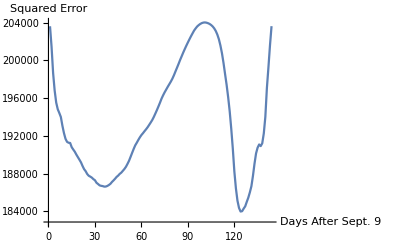
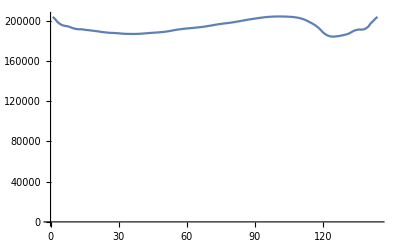

```mathematica
Timing[period5Data = Take[sinceJune2020,{101, Length[sinceJune2020]}];
fitPeriod5Table=ParallelTable[{date,NMinimize[Total[(period5Data-period5Cycle * Table[twoExpFunc[t, date,c1, r1,r2],{t, Length[period5Data]}])^2], {c1,r1,r2,w1,w2,w3,w4,w5,w6,w7},Method->"DifferentialEvolution"]},{date,2,Length[period5Data]-1}];]
squaredErrors=Map[First,Map[Last,fitPeriod5Table]];
bestPeriod5break =Position[squaredErrors,Min[squaredErrors]][[1,1]]
bestPeriod5Params=fitPeriod5Table[[bestPeriod5break,2,2]] 
squaredErrors[[ bestPeriod5break ]];
doubleHalfTimes= Log[2.]/{r1,r2} /.bestPeriod5Params
{ListPlot[ Map[First,Map[Last,fitPeriod5Table]],PlotRange->Automatic,Joined->True ,AxesLabel->{"Days After Sept. 9","Squared Error"}],
ListPlot[ Map[First,Map[Last,fitPeriod5Table]],PlotRange->{0,All},Joined->True ]}
```

## FIT USING BEST BREAKPOINT

{{0.0051343,-0.0216221},1.01786
0.928153,135.
-32.1,{73,58,78,103,98,97,80,63,50,67,89,84,84,69,54}}

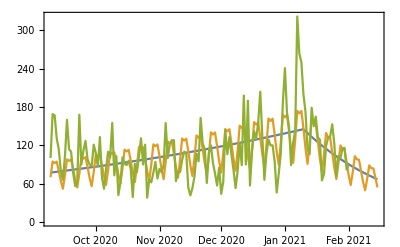

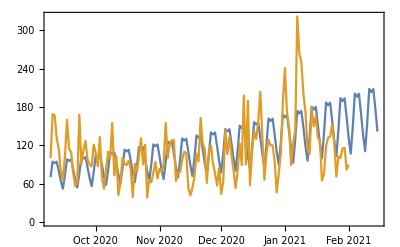

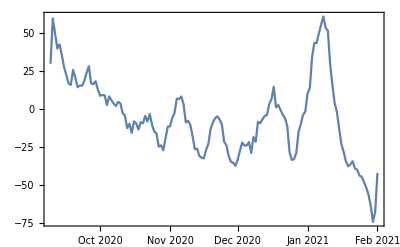

```mathematica
period5CycProj =  Take[Flatten[Table[{w1,w2,w3,w4,w5,w6,w7},2+ Ceiling[Length[period5Data]/7]]],Length[period5Data]+14];
period5FitTabProj= (period5CycProj * Table[twoExpFunc[t,bestPeriod5break, c1, r1,r2],{t, Length[period5Data]+14}]) /.bestPeriod5Params;
period5FuncProj= (Mean@period5CycProj * Table[twoExpFunc[t,bestPeriod5break, c1, r1,r2],{t, Length[period5Data]+14}]) /.bestPeriod5Params;
period5FitTabCont= (period5CycProj * Table[twoExpFunc[t,bestPeriod5break, c1, r1,r1],{t, Length[period5Data]+14}]) /.bestPeriod5Params;
{{r1,r2}/.bestPeriod5Params,TF@Map[rToRt,{r1,r2}/.bestPeriod5Params],TF@Round[Map[rToDoublingTime,{r1,r2}/.bestPeriod5Params],0.1],Round[Take[period5FitTabProj,-15],1]}
(* LPJ@{period5FuncProj,period5FitTabProj,period5Data} *)
DateListPlot[Map[TimeSeries[#,{"Sep 9, 2020"}]&,{period5FuncProj,period5FitTabProj,period5Data}],PlotRange->All,GridLines->True ]
DateListPlot[Map[TimeSeries[#,{"Sep 9, 2020"}]&,{period5FitTabCont,period5Data}],PlotRange->All,GridLines->True ]
DateListPlot[TimeSeries[runningSymMean[period5Data -Take[period5FitTabCont,Length[period5Data]],7],{"Sep 9, 2020"}],PlotRange->All,GridLines->{True,{0}}]
(* ListPlot[{period5Data,period5FitTabCont},Joined->True,AxesLabel->{"Days after Sept. 9","Cases"}]
ListPlot[period5Data -Take[period5FitTabCont,Length[period5Data]],Joined->True,AxesLabel->{"Days after Sept. 9","Excess in cases"}] *)
(* ListPlot[runningSymMean[period5Data -Take[period5FitTabCont,Length[period5Data]],7],Joined->True,AxesLabel->{"Days after Sept. 9","Smoothed excess in cases"}] *)
```